### Zadatak1

```mathematica
tacke ={{1, 1}, {2,5}, {3,14},{5,81}}
```

{{1,1},{2,5},{3,14},{5,81}}

```mathematica
p1[x_]=InterpolatingPolynomial[tacke,x]
```

```mathematica
1+(4+(5/2+17/12 (-3+x)) (-2+x)) (-1+x)
Simplify[%]
```

1+(4+(5/2+17/12 (-3+x)) (-2+x)) (-1+x)

```mathematica
1/12 (-78+145 x-72 x^2+17 x^3)
```

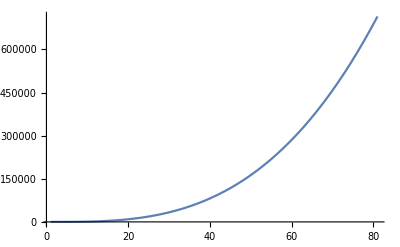

```mathematica
c=Plot[p1[x], {x, 1, 81}]
```

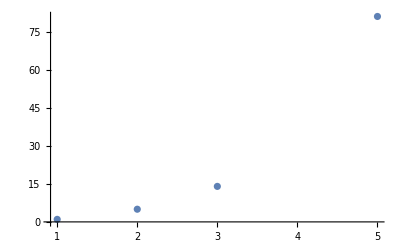

```mathematica
t = ListPlot[{{1, 1}, {2,5}, {3,14},{5,81}}]
```

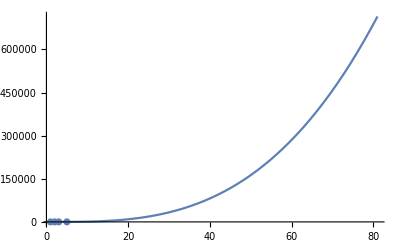

```mathematica
Show[c, t]
```

### Zadatak2

```mathematica
tacke2 ={{7, 3}, {8,1}, {9,1},{10,9}}
Map[y, {7,8,9,10}]
```

### Zadatak3

```mathematica
tacke =List [100,121,144]
```

```mathematica
{100,121,144}
Part[tacke, 1]
```

{100,121,144}

100

```mathematica
Map[√i, {100, 121, 144}]
```

{√i[100],√i[121],√i[144]}

```mathematica
rez[x_]= ∑_(i=1)^3 (√tacke[[i]]* ∏_(j=1)^3 (If[j≠ i,(x-Part[tacke,j])/ (Part[tacke,i]-Part[tacke,j]) , 1]))
```

5/462 (121-x) (144-x)+11/483 (144-x) (-100+x)+3/253 (-121+x) (-100+x)

```mathematica
Simplify[%]
```

(43560+727 x-x^2)/10626

```mathematica
L =rez[117]
```

19155/1771

```mathematica
f= √117
```

3 √13

```mathematica
greska = Abs[N[L]-N[f]]
```

0.000730619

### Zadatak4

```mathematica
tacke4=List [0.2,0.9,1.7,2.3]
```

{0.2,0.9,1.7,2.3}

```mathematica
Map[i*Log[i]+i*E^-i, {0.2,0.9,1.7,2.3}]
```

{(ⅇ^-i i+i Log[i])[0.2],(ⅇ^-i i+i Log[i])[0.9],(ⅇ^-i i+i Log[i])[1.7],(ⅇ^-i i+i Log[i])[2.3]}

```mathematica
rez4[x_]= ∑_(i=1)^3 (√tacke4[[i]]* ∏_(j=1)^3 (If[j≠ i,(x-Part[tacke4,j])/ (Part[tacke4,i]-Part[tacke4,j]) , 1])) //Simplify
```

0.271244+0.916174 x-0.181626 x^2

```mathematica
L4= rez4[1.9]
```

1.3563

```mathematica
f= 0.9*Log[0.9] + 0.9*E^0.9
```

2.11882

```mathematica
greska4=Abs[N[L]-N[f]]
```

8.6971

### Zadatak5

```mathematica
Table[{x, e^-x}, {x, 1, 2, 3}]
```

{{1,1/e}}

### Zadatak6

```mathematica
Table[{x, Log[x]-(x-1)/x}, {x, 2, 4, 6, 10}]
```

Table::itform: Argument {x,2,4,6,10} at position 2 does not have the correct form for an iterator.

Table[{x,Log[x]-(x-1)/x},{x,2,4,6,10}]

```mathematica
Sum[√i* Product[If[j≠i,(x-tacke[j])/ (tacke[i]-tacke[j]),1 ],{j,0,2}]]
```